# Notebook for : Spacetime Embedding Diagrams for Black Holes by Marolf

Geoff Cope
University of Utah
															𐐏𐐭𐑌𐐲𐑂𐐲𐑉𐑅𐐮𐐻𐐨 𐐲𐑂 𐐏𐐭𐐻𐐫
February 24, 2021

## Hyperlink To Documentation

```mathematica
Hyperlink["GeneralRelativityTensors Documentation and Download",
"https://github.com/BlackHolePerturbationToolkit"]
```

[GeneralRelativityTensors Documentation and Download](https://github.com/BlackHolePerturbationToolkit)

## Hyperlink To Article

```mathematica
Hyperlink["Spacetime Embedding Diagrams for Black Holes by Marolf",
"https://arxiv.org/abs/gr-qc/9806123"]
```

[Spacetime Embedding Diagrams for Black Holes by Marolf](https://arxiv.org/abs/gr-qc/9806123)

## Utilities and Package Load

```mathematica
ClearAll["Global`*"]
<<Utilities`CleanSlate`
CleanSlate[]
ClearInOut[]

pdConv[f_]:=TraditionalForm[f/.Derivative[inds__][g_][vars__]:>Apply[Defer[D[g[vars],##]]&,Transpose[{{vars},{inds}}]/.{{var_,0}:>Sequence[],{var_,1}:>{var}}]]
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 7 Kb

{Utilities`CleanSlate`,DocumentationSearch`,ResourceLocator`,System`,Global`}

```mathematica
<<GeneralRelativityTensors`
```

## Custom Notation

```mathematica
Clear[dtReplace]
dtReplace = {
Dt[Subscript[Z, 0]] -> Subscript[dZ, 0] ,
Dt[Subscript[Z, 1]] -> Subscript[dZ, 1] ,
Dt[Subscript[Z, 2]]-> Subscript[dZ, 2] ,
Dt[Subscript[Z, 3]]-> Subscript[dZ, 3] ,
Dt[Subscript[Z, 4]] -> Subscript[dZ, 4] ,
 Dt[Subscript[η, 0]]-> Subscript[dη, 0] , 
 Dt[Subscript[t, 0]]-> Subscript[dt, 0] , 
 Dt[t]-> dt ,
 Dt[T]-> dT ,
Dt[X]-> dX , 
Dt[Z]-> dZ , 
Dt[ξ]-> dξ , 
Dt[ψ]-> dψ , 
Dt[χ] -> dχ , 
 Dt[θ] -> dθ , 
Dt[ϕ] -> dϕ  ,
Dt[φ]-> dφ , 
Dt[η] -> dη  ,
Dt[R] -> dR  ,
Dt[b]-> db , 
Dt[r]-> dr , 
Dt[u]-> du , 
Dt[v]-> dv , 
Dt[x]-> dx , 
Dt[y] -> dy , 
Dt[z]-> dz  ,
Dt[𝓊]-> d𝓊 , 
Dt[𝓍]-> d𝓍 , 
Dt[Subscript[t, -1]]-> Subscript[dt, -1] , 
Dt[Subscript[t, b]]-> Subscript[dt, b] ,
Dt[Subscript[z, b]]-> Subscript[dz, b] ,
Dt[Subscript[t, k]] -> Subscript[dt, k] ,
Dt[Subscript[z, k]] -> Subscript[dz, k] ,
Dt[τ]-> dτ ,  
Dt[ρ] -> dρ 
} ;
dtReplace // TableForm
```

Dt[Z] Subscript^(1,0)[Z,0]→dZ_0
Dt[Z] Subscript^(1,0)[Z,1]→dZ_1
Dt[Z] Subscript^(1,0)[Z,2]→dZ_2
Dt[Z] Subscript^(1,0)[Z,3]→dZ_3
Dt[Z] Subscript^(1,0)[Z,4]→dZ_4
Dt[η] Subscript^(1,0)[η,0]→dη_0
Dt[t] Subscript^(1,0)[t,0]→dt_0
Dt[t]→dt
Dt[T]→dT
Dt[X]→dX
Dt[Z]→dZ
Dt[ξ]→dξ
Dt[ψ]→dψ
Dt[χ]→dχ
Dt[θ]→dθ
Dt[ϕ]→dϕ
Dt[φ]→dφ
Dt[η]→dη
Dt[R]→dR
Dt[b]→db
Dt[r]→dr
Dt[u]→du
Dt[v]→dv
Dt[x]→dx
Dt[y]→dy
Dt[z]→dz
Dt[𝓊]→d𝓊
Dt[𝓍]→d𝓍
Dt[t] Subscript^(1,0)[t,-1]→dt_-1
Dt[b] Subscript^(0,1)[t,b]+Dt[t] Subscript^(1,0)[t,b]→dt_b
Dt[b] Subscript^(0,1)[z,b]+Dt[z] Subscript^(1,0)[z,b]→dz_b
Dt[k] Subscript^(0,1)[t,k]+Dt[t] Subscript^(1,0)[t,k]→dt_k
Dt[k] Subscript^(0,1)[z,k]+Dt[z] Subscript^(1,0)[z,k]→dz_k
Dt[τ]→dτ
Dt[ρ]→dρ

```mathematica
(* b/:Dt[b]=0  ;  *)  (* for transform 37 *)
```

```mathematica
rs/:Dt[rs]=0   ;(* Schwarzschild radius equation 2.2.35 *) 
rg/:Dt[rg]=0   ;  
α/:Dt[α]=0   ; (* De Sitter equation 2.21.9 *) 
ω/:Dt[ω]=0   ;  (* 2.2.28 *)
```

## Line Element and Metric Functions

```mathematica
Clear[lineToMetric]
lineToMetric[lineelement_ , differentials_]:= 
Table[If[i==j ,Coefficient[lineelement, differentials[[i]] differentials[[j]]],
(1/2)*Coefficient[lineelement, differentials[[i]] differentials[[j]]]],
{i,1,Length[differentials]},{j,1,Length[differentials]}]  ;
```

```mathematica
Clear[metricToLine]
metricToLine[metric_, differentials_]:= 
Sum[metric[[i,j]] differentials[[i]] differentials[[j]] , {i,1,Length[differentials]},{j,1,Length[differentials]}]
```

## Line Element and Metric 2.1 Schwarzschild

```mathematica
Clear[eq2pt1]
eq2pt1 = 
-c^2( 1 - (2 M G)/(r c^2)) dt^2 + dr^2/(1 - ((2 M G)/(r c^2)))+ r^2 dθ^2 + r^2 Sin[θ]^2 dϕ^2 /. c-> 1 /. G-> 1  /. M-> 1/2 (* see unit convention description figure 7 *)
```

dr^2/(1-1/r)-dt^2 (1-1/r)+dθ^2 r^2+dϕ^2 r^2 Sin[θ]^2

```mathematica
Clear[metric2pt1]
metric2pt1 = 
lineToMetric[ eq2pt1 , {dt,dr,dθ,dϕ}]  ;
metric2pt1 // MatrixForm
```

(-1+1/r | 0 | 0 | 0
0 | 1/(1-1/r) | 0 | 0
0 | 0 | r^2 | 0
0 | 0 | 0 | r^2 Sin[θ]^2)

## Minkowski Metric

```mathematica
Clear[minkowski]
minkowski = 
-dT^2+ dX^2+ dY^2+ dZ^2
```

-dT^2+dX^2+dY^2+dZ^2

```mathematica
lineToMetric[ minkowski , {dT,dX,dY,dZ}] // MatrixForm
```

(-1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

## Appendix A

```mathematica
Clear[A1]
A1 = 
-c^2( 1 - (2 M G)/(r c^2)) dt^2 + dr^2/(1 - ((2 M G)/(r c^2)))+ r^2 dθ^2 + r^2 Sin[θ]^2 dϕ^2 /. dθ-> 0 /. dϕ-> 0 /. c-> 1 /. G-> 1
```

dr^2/(1-(2 M)/r)-dt^2 (1-(2 M)/r)

```mathematica
lineToMetric[ A1 , {dt,dr}] // MatrixForm
```

(-1+(2 M)/r | 0
0 | 1/(1-(2 M)/r))

```mathematica
Clear[A2]
A2 = {
ρ == √(X^2- T^2)  , 
ϕ ==ArcTanh[ T/X]
} ;
A2  // TableForm
```

ρ==√(-T^2+X^2)
ϕ==ArcTanh[T/X]

```mathematica
Solve[ A2 , {T,X}][[2]]  // TableForm
```

T→(ρ Tanh[ϕ])/(√(1-Tanh[ϕ]^2))
X→ρ/(√(1-Tanh[ϕ]^2))

```mathematica
Dt[ Solve[ A2 , {T,X}][[2]] ]  /. dtReplace  // Expand // Simplify // PowerExpand  // TableForm
```

dT→Cosh[ϕ] (dϕ ρ+dρ Tanh[ϕ])
dX→Cosh[ϕ] (dρ+dϕ ρ Tanh[ϕ])

```mathematica
Clear[A3]
A3 = 
minkowski /. ( Dt[ Solve[ A2 , {T,X}][[2]] ]  /. dtReplace  // Expand // Simplify // PowerExpand  )  /. dZ-> 0 // Expand // Simplify
```

dY^2+dρ^2-dϕ^2 ρ^2

```mathematica
lineToMetric[ A3 , {dϕ,dρ,dY}] // MatrixForm
```

(-ρ^2 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

```mathematica
Clear[A3pt1]
A3pt1 = 
ρ[r] == 4 M √(1- (2 M)/r)
```

ρ[r]==4 M √(1-(2 M)/r)

```mathematica
D[ A3pt1 , r ] /. Equal-> Rule
```

ρ'[r]→(4 M^2)/(√(1-(2 M)/r) r^2)

```mathematica
Clear[A4]
A4 = 
( A1 /. dt-> 0 )== (A3 /. dϕ-> 0 )
```

dr^2/(1-(2 M)/r)==dY^2+dρ^2

```mathematica
Apart[Assuming[ dr^2 ≠ 0  , DivideSides[ A4  , dr^2]]]
```

1+(2 M)/(-2 M+r)==dY^2/dr^2+dρ^2/dr^2

```mathematica
Apart[Assuming[ dr^2 ≠ 0  , DivideSides[ A4  , dr^2]]]  /.  dY-> Y'[r] dr
```

1+(2 M)/(-2 M+r)==dρ^2/dr^2+Y'[r]^2

```mathematica
Clear[A5pt1]
A5pt1 = 
(Apart[Assuming[ dr^2 ≠ 0  , DivideSides[ A4  , dr^2]]]  /.  dY-> Y'[r] dr  ) /. ( dρ-> ρ'[r] dr /.(D[ A3pt1 , r ] /. Equal-> Rule   ) )
```

1+(2 M)/(-2 M+r)==(16 M^4)/((1-(2 M)/r) r^4)+Y'[r]^2

```mathematica
Clear[A5]
A5 = 
Flatten[Solve[ A5pt1  , Y'[r]]][[2]] /. Rule-> Equal
```

Y'[r]==(√(8 M^3+4 M^2 r+2 M r^2+r^3))/r^(3/2)

```mathematica
Clear[ySolution]
ySolution = 
Flatten[NDSolve[ {(A5 /. M-> 1), Y[2]== 2}  , Y[r] , {r,2,5}]]
```

{Y[r]→InterpolatingFunction[…][r]}

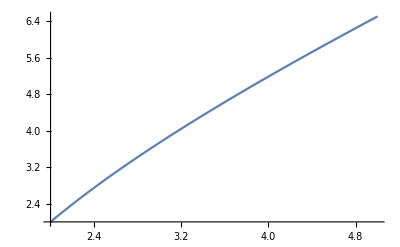

```mathematica
Plot[ Y[r] /. ySolution  , {r,2,5}]
```

## Appendix B

```mathematica
Clear[B1]
B1 = 
- Exp[2Φ] dt^2+ dr^2/(1-(2 m[r])/r)+ r^2 dΩ^2
```

-dt^2 ⅇ^(2 Φ)+dΩ^2 r^2+dr^2/(1-(2 m[r])/r)

```mathematica
Clear[B1pt1]
B1pt1 = 
m[r] == ∫_0^r 4 π  𝓇^2 ρ[𝓇]ⅆ𝓇
```

m[r]==∫_0^r 4 π 𝓇^2 ρ[𝓇]ⅆ𝓇

```mathematica
D[ B1pt1  , r ]
```

m'[r]==4 π r^2 ρ[r]

```mathematica
Clear[B2]
B2 = 
Φ'[r] == (m + r π r^3 p)/(r(r-2 m )) (* is pressure constant or p[r]? *)
```

Φ'[r]==(m+p π r^4)/(r (-2 m+r))